# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización para un elipsoide

```mathematica
f[q_,a_,b_,c_]:=Sqrt[(a^2+q)(b^2+q)(c^2+q)]
```

```mathematica
l[j_,a_,b_,c_]:=Module[{n= a b c *0.5},
				Which[j==1,n*NIntegrate[1/((a^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==2,n*NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}],
					j==3,n*NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

Redefiniendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[j_,a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2)},Which[j==1|| j==2,(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2),
						j==3,(a^2 c)/2* NIntegrate[1/((c^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
elipsprolato[j_,a_,b_,c_]:=Module[{eab2=1-(b^2/a^2)},Which[j==1,((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]),
						j==2||j==3,(a^2 b)/2 *NIntegrate[1/((b^2+q) (f[q,a,b,c])),{q,0,Infinity}]]]
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[j,a,b,c],
							b==c ,elipsprolato[j,a,b,c],True,l[j,a,b,c]]
```

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
N[factgeom[1,10,15,15]]
```

0.445906+5.7814×10^-17 ⅈ

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

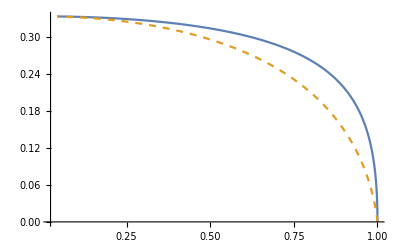

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo las secciones transversales de extinción, absorción y esparcimiento

```mathematica
Cext[j_,a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,α,Cext,Qext},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										α=4 π a b c ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[j,a,b,c] (ϵp-ϵm)));
										Cext=k Im[α];Qext=Which[j==1,Cext/(Pi*(b c)),j==2 ,Cext/(Pi*( a c)),j==3,Cext/(Pi*(a b))];
										{Cext,Qext}]
```

```mathematica
Csca[j_,a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,α,Csca,Qsca},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										α=4 π a b c ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[j,a,b,c] (ϵp-ϵm)));
										Csca=(Norm[α]^2* k^4)/6 π;
										Qsca=Which[j==1,Csca/(Pi*(b c)),j==2 ,Csca/(Pi*( a c)),j==3,Csca/(Pi*(a b))];
{Csca,Qsca}]

Cabs[j_,a_,b_,c_,nm_,λ_,λp_,γ_]:=Cext[j,a,b,c,nm,λ,λp,γ]-Csca[j,a,b,c,nm,λ,λp,γ]
```

### Datos experimentales

```mathematica
Cextexp[j_,a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,α,Cext,Qext},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										α=4 π a b c ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[j,a,b,c] (ϵp-ϵm)));
										Cext=k Im[α];
										Qext=Which[j==1,Cext/(Pi*(b c)),j==2 ,Cext/(Pi*( a c)),j==3,Cext/(Pi*(a b))];
										{Cext,Qext}]
```

```mathematica
Cscaexp[j_,a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,α,Csca,Qsca},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										α=4 π a b c ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[j,a,b,c] (ϵp-ϵm)));
										Csca=(Norm[α]^2* k^4)/6 π;
										Qsca=Which[j==1,Csca/(Pi*(b c)),j==2 ,Csca/(Pi*( a c)),j==3,Csca/(Pi*(a b))];
{Csca,Qsca}]

Cabsexp[j_,a_,b_,c_,nm_,λ_,np_]:=Cextexp[j,a,b,c,nm,λ,np][[2]]-Cscaexp[j,a,b,c,nm,λ,np][[2]]
```

## Cálculos

### Función dieléctrica tipo Drude

#### Para ℏω = 4.3 eV, ℏγ = 0.15 eV, nm = 1.33, a = b = 5 nm, c=7 nm

```mathematica
qextDrude1=Table[{λ,Cext[1,25,20,30,1.33,λ,2 Pi vlight/(4.3/ℏ),(0.15/ℏ)][[2]]},{λ,100,1000}];
qextDrude2=Table[{λ,Cext[2,25,20,30,1.33,λ,2 Pi vlight/(4.3/ℏ),(0.15/ℏ)][[2]]},{λ,100,1000}];
qextDrude3=Table[{λ,Cext[3,25,20,30,1.33,λ,2 Pi vlight/(4.3/ℏ),(0.15/ℏ)][[2]]},{λ,100,1000}];
```

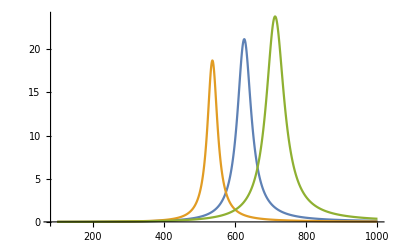

```mathematica
ListLinePlot[{qextDrude1,qextDrude2,qextDrude3},PlotRange->All]
```

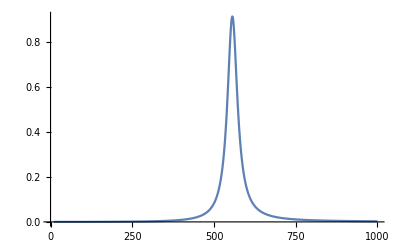

```mathematica
qextDrude1=Table[{λ,Cext[3,15,15,12,1.33,λ,2 Pi vlight/(4.3/ℏ),(0.15/ℏ)][[2]]},{λ,10,1000}];
ListLinePlot[{qextDrude1},PlotRange->All]
```

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[alum,{208,415}].

Part::partd: Part specification {208,415}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {208,415}⟦All,2⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[alum,{1,209}].

Part::partd: Part specification Drop[alum,{1,209}]⟦All,2⟧ is longer than depth of object.

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
Qextalum[j_,a_,b_,c_,nm_,λ_,λp_,γ_]:=Cext[j,a,b,c,nm,λ,λp,γ][[2]]+Csca[j,a,b,c,nm,λ,λp,γ][[2]]
```

Para esferoides oblatos (a=b > c y L1=L2)

```mathematica
QextAl1ob=Table[{λ,Cextalum[1,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[1]]},{λ,130,250}];
QscaAl1ob=Table[{λ,Csca[1,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[1]]},{λ,130,250}];
QabsAl1ob=Table[{λ,Cext[1,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[1]]},{λ,130,250}];
QextAl2ob=Table[{λ,Cextalum[2,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
QscaAl2ob=Table[{λ,Csca[2,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
QabsAl2ob=Table[{λ,Cext[2,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
QextAl3ob=Table[{λ,Cextalum[3,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
QscaAl3ob=Table[{λ,Csca[3,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
QabsAl3ob=Table[{λ,Cext[3,15,15,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,130,250}];
```

```mathematica
upperTicksAl1=Module[{labels,positions},labels={4.6,5.1,5.8,7,8,9,11};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl1=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

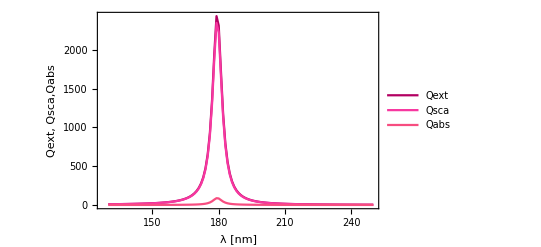

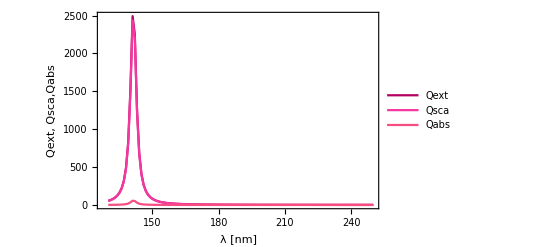

```mathematica
drudeAl1=ListLinePlot[{Style[QextAl1ob,RGBColor[0.702,0,0.384]],Style[QscaAl1ob,RGBColor[0.969,0.216,0.627]],Style[QabsAl1ob,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
drudeAl2=ListLinePlot[{Style[QextAl3ob,RGBColor[0.702,0,0.384]],Style[QscaAl3ob,RGBColor[0.969,0.216,0.627]],Style[QabsAl3ob,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

```mathematica
Export["alumninio.pdf",al1]
```

alumninio.pdf

Para esferoides prolatos (b=c y L2=L3)

```mathematica
QextAl1pr=Table[{λ,Cextalum[1,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,300}];
QscaAl1pr=Table[{λ,Csca[1,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,300}];
QabsAl1pr=Table[{λ,Cext[1,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,250}];
QextAl3pr=Table[{λ,Cextalum[3,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,300}];
QscaAl3pr=Table[{λ,Csca[3,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,300}];
QabsAl3pr=Table[{λ,Cext[3,15,10,10,1,λ,2 Pi vlight/(13.142/ℏ),(0.197/ℏ)][[2]]},{λ,100,250}];
```

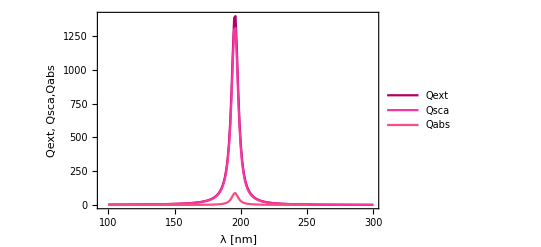

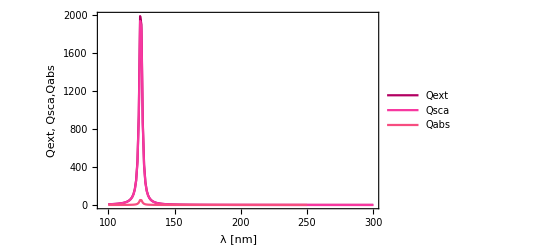

```mathematica
drudeAl3=ListLinePlot[{Style[QextAl1pr,RGBColor[0.702,0,0.384]],Style[QscaAl1pr,RGBColor[0.969,0.216,0.627]],Style[QabsAl1pr,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
drudeAl4=ListLinePlot[{Style[QextAl3pr,RGBColor[0.702,0,0.384]],Style[QscaAl3pr,RGBColor[0.969,0.216,0.627]],Style[QabsAl3pr,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

#### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en nm*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

```mathematica
nindexau=Interpolation[aU];
```

Para esferoides oblatos (a=b > c y L1=L2)

```mathematica
QextAu1ob=Table[{λ,Cextexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAu1ob=Table[{λ,Cscaexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QabsAu1ob=Table[{λ,-Cextexp[1,15,15,10,1,λ,nindexau[λ]][[2]]+Cscaexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAu3ob=Table[{λ,Cextexp[3,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAu3ob=Table[{λ,Cscaexp[3,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QabsAu3ob=Table[{λ,-Cextexp[3,15,15,10,1,λ,nindexau[λ]][[2]]+Cscaexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
```

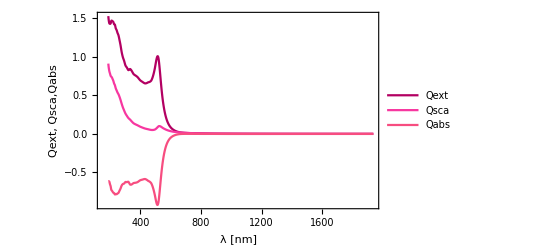

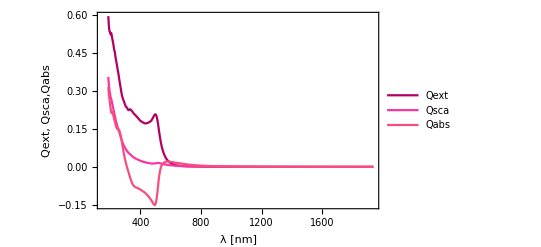

```mathematica
drudeAu1=ListLinePlot[{Style[QextAu1ob,RGBColor[0.702,0,0.384]],Style[QscaAu1ob,RGBColor[0.969,0.216,0.627]],Style[QabsAu1ob,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
drudeAu2=ListLinePlot[{Style[QextAu3ob,RGBColor[0.702,0,0.384]],Style[QscaAu3ob,RGBColor[0.969,0.216,0.627]],Style[QabsAu3ob,RGBColor[0.969,0.3,0.5]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],FrameLabel->{{Style["Qext, Qsca,Qabs",Black,12],None},{Style["λ [nm]",Black,12],Style["ℏω [eV]",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl1,upperTicksAl1]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Qext","Qsca","Qabs"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&)],{0.8,0.7}]]
```

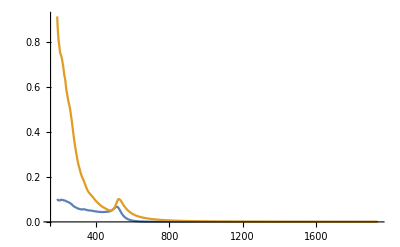

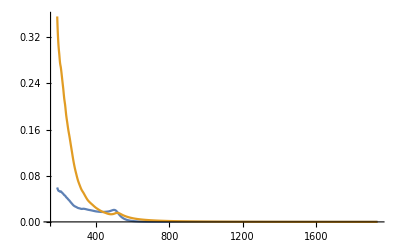

```mathematica
ListLinePlot[{QextAu1ob,QscaAu1ob},PlotRange->All]
ListLinePlot[{QextAu3ob,QscaAu3ob},PlotRange->All]
```

Para esferoides prolatos (b=c y L2=L3)

```mathematica
QextAu1pr=Table[{(h vlight)/λ,Cextexp[1,15,10,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAu1pr=Table[{(h vlight)/λ,Cscaexp[1,15,10,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAu3pr=Table[{(h vlight)/λ,Cextexp[3,15,10,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAu3pr=Table[{(h vlight)/λ,Cscaexp[3,15,10,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
```

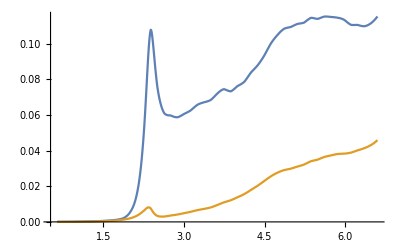

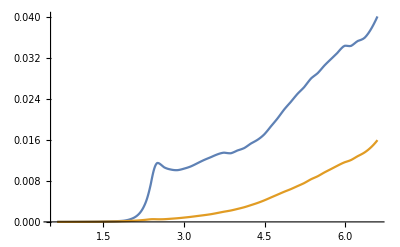

```mathematica
ListLinePlot[{QextAu1pr,QscaAu1pr},PlotRange->All]
ListLinePlot[{QextAu3pr,QscaAu3pr},PlotRange->All]
```

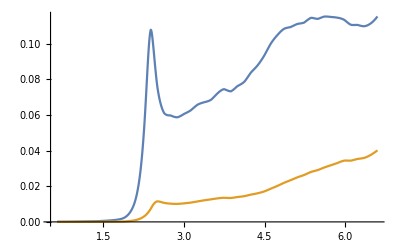

```mathematica
ListLinePlot[{QextAu1pr,QextAu3pr},PlotRange->All]
```

Comparación entre prolato y oblato

```mathematica
QextAuob1=Table[{(h vlight)/λ,Cextexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAupr1=Table[{(h vlight)/λ,Cextexp[1,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAuob1=Table[{(h vlight)/λ,Cscaexp[1,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAupr1=Table[{(h vlight)/λ,Cscaexp[1,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAuob2=Table[{(h vlight)/λ,Cextexp[2,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAupr2=Table[{(h vlight)/λ,Cextexp[2,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAuob2=Table[{(h vlight)/λ,Cscaexp[2,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAupr2=Table[{(h vlight)/λ,Cscaexp[2,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAuob3=Table[{(h vlight)/λ,Cextexp[3,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QextAupr3=Table[{(h vlight)/λ,Cextexp[3,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAuob3=Table[{(h vlight)/λ,Cscaexp[3,15,15,10,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
QscaAupr3=Table[{(h vlight)/λ,Cscaexp[3,10,15,15,1,λ,nindexau[λ]][[2]]},{λ,188,1937}];
```

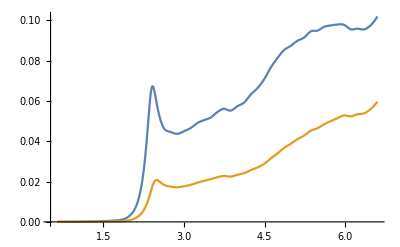

```mathematica
ListLinePlot[{QextAuob1,QextAupr1},PlotRange->All]
```

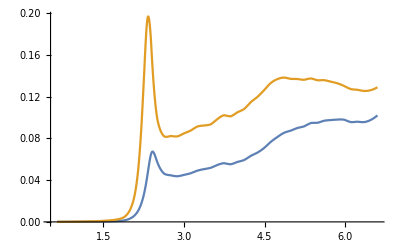

```mathematica
ListLinePlot[{QextAuob2,QextAupr2},PlotRange->All]
```

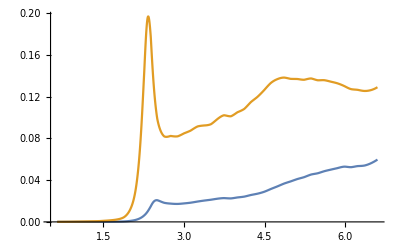

```mathematica
ListLinePlot[{QextAuob3,QextAupr3},PlotRange->All]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
(*ag=Import["C:\\Users\\Lunita\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

```mathematica
QextAg1=Table[{λ,Cextexp[1,15,10,10,1,λ,nindexplata[λ]][[2]]},{λ,188,1937}];
QextAg2=Table[{λ,Cextexp[2,15,10,10,1,λ,nindexplata[λ]][[2]]},{λ,188,1937}];
QextAg3=Table[{λ,Cextexp[3,15,10,10,1,λ,nindexplata[λ]][[2]]},{λ,188,1937}];
```

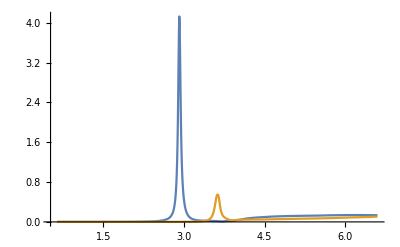

```mathematica
ListLinePlot[{QextAg1,QextAg3},PlotRange->All]
```

#### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
QextBis1=Table[{(h vlight)/λ,Cextexp[1,0.15,.10,.10,1.33,λ,nindexbismuto[λ]][[2]]},{λ,10,619.9}];
QextBis2=Table[{(h vlight)/λ,Cextexp[2,15,10,10,1.33,λ,nindexbismuto[λ]][[2]]},{λ,2.48*10^(-3),619.9}];
QextBis3=Table[{(h vlight)/λ,Cextexp[3,15,10,10,1.33,λ,nindexbismuto[λ]][[2]]},{λ,2.48*10^(-3),619.9}];
```

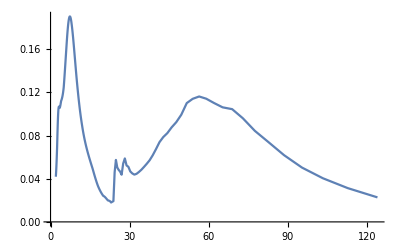

```mathematica
ListLinePlot[{QextBis1},PlotRange->All]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

```mathematica
QextMgO1=Table[{(h vlight)/λ,Cextexp[1,15,10,10,1.33,λ,nindexMgO[λ]][[2]]},{λ,360,5400}];
QscaMgO2=Table[{(h vlight)/λ,Cscaexp[1,15,10,10,1.33,λ,nindexMgO[λ]][[2]]},{λ,360,5400}];
QextMgO3=Table[{(h vlight)/λ,Cextexp[3,15,10,10,1.33,λ,nindexMgO[λ]][[2]]},{λ,360,5400}];
```

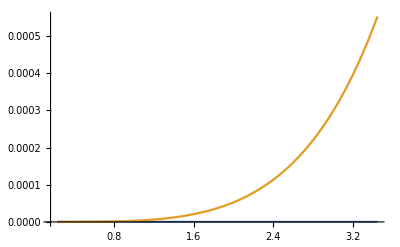

```mathematica
ListLinePlot[{QextMgO1,QscaMgO2},PlotRange->All]
```